```mathematica
(*  1. Группировка данных *)
FindC[start_,end_,seq_] :=(
nn = Length[seq];
count = 0;
For[j =1, j≤nn,j++,
If[seq[[j]] ≥ start && seq[[j]] < end, count++];
If[seq[[j]]  ≥ end, Break[]];
];
Return[count];
);

x = {3.22,2.58,3.03,2,2.53,2.61,1.87,4.41,4.48,3.10,
4.99,1.82,3.3,2.93,1.16,4.12,2.1,2.47,4.16,2.14,
2.89,1.94,3.29,2.98,3.75,2.51,3.17,4.43,2.83,3.56,
4.36,1.64,2.74,4.13,5.13,2.44,2.51,3.97,2.86,2.96,
2.99,2.77,2.43,2.24,4.34,3.05,2.53,2.25,3.64,3.45};
x = Sort[x];
Print["sort ",x];
n = Length[x];
Print["n=",n];
Δt = (x[[n]] - x[[1]])/(1+ Log[2,n]);
Print["Δt  = ", Δt ];
NN = Ceiling[(x[[n]] - x[[1]])/ Δt];
Print["N=",NN];
first = Table[{}, {i,NN},{j,6}];
For[i = 1, i≤ NN,i++,
first[[i,1]] = i;
first[[i,2]] = x[[1]] + (i-1) * Δt;
If[i≠NN,first[[i,3]] = x[[1]] + i * Δt,first[[i,3]] = x[[n]] ];
first[[i,4]] = (first[[i,2]]  + first[[i,3]])/2 ;
first[[i,5]] = FindC[first[[i,2]] ,first[[i,3]] ,x];
If[i == NN , first[[i,5]] ++];
first[[i,6]] = first[[i,5]]/n;
];
Print[TableForm[first,TableHeadings->{None,{"№","Начало","Конец","Середина","Частота","Частость"}}]];
```

sort {1.16,1.64,1.82,1.87,1.94,2,2.1,2.14,2.24,2.25,2.43,2.44,2.47,2.51,2.51,2.53,2.53,2.58,2.61,2.74,2.77,2.83,2.86,2.89,2.93,2.96,2.98,2.99,3.03,3.05,3.1,3.17,3.22,3.29,3.3,3.45,3.56,3.64,3.75,3.97,4.12,4.13,4.16,4.34,4.36,4.41,4.43,4.48,4.99,5.13}

n=50

Δt  = 0.597545

N=7

№ | Начало | Конец | Середина | Частота | Частость
1 | 1.16 | 1.75754 | 1.45877 | 2 | 1/25
2 | 1.75754 | 2.35509 | 2.05632 | 8 | 4/25
3 | 2.35509 | 2.95263 | 2.65386 | 15 | 3/10
4 | 2.95263 | 3.55018 | 3.25141 | 11 | 11/50
5 | 3.55018 | 4.14772 | 3.84895 | 6 | 3/25
6 | 4.14772 | 4.74527 | 4.44649 | 6 | 3/25
7 | 4.74527 | 5.13 | 4.93763 | 2 | 1/25

```mathematica
Np = NN - 2;
second =  Table[{}, {i,Np},{j,6}];
second[[1,1]] = 1;
second[[1,2]] = x[[1]] ;
second[[1,3]] = first[[2,3]] ;
second[[1,4]] = (second[[1,2]]  + second[[1,3]])/2 ;
second[[1,5]] = first[[1,5]] +first[[2,5]] ;
second[[1,6]] = second[[1,5]]/n;
For[i = 2,i≤ Np-1, i++,
second[[i,1]] = i;
second[[i,2]] = first[[i + 1,2]] ;
second[[i,3]] = first[[i + 1,3]] ;
second[[i,4]] = first[[i + 1,4]] ;
second[[i,5]] = first[[i + 1,5]] ;
second[[i,6]] =first[[i + 1,6]] ;
];

second[[Np,1]] = Np;
second[[Np,2]] = first[[NN - 1,2]] ;
second[[Np,3]] = first[[NN,3]];
second[[Np,4]] = (second[[Np,2]]  + second[[Np,3]])/2 ;
second[[Np,5]] = first[[Np + 1,5]] +first[[Np + 2,5]] ;
second[[Np,6]] = second[[Np,5]]/n;
Print[TableForm[second,TableHeadings->{None,{"№","Начало","Конец","Середина","Частота","Частость"}}]];
```

№ | Начало | Конец | Середина | Частота | Частость
1 | 1.16 | 2.35509 | 1.75754 | 10 | 1/5
2 | 2.35509 | 2.95263 | 2.65386 | 15 | 3/10
3 | 2.95263 | 3.55018 | 3.25141 | 11 | 11/50
4 | 3.55018 | 4.14772 | 3.84895 | 6 | 3/25
5 | 4.14772 | 5.13 | 4.63886 | 8 | 4/25

```mathematica
(*  2. *)
```

```mathematica
a = 0;
a = (∑_(i=1)^Np second[[i,4]] * second[[i,5]])/n;
Print["a=",a];
```

a=3.06707

```mathematica
d = (∑_(i=1)^Np ((second[[i,4]]  - a)^2* second[[i,5]]))/n;
Print["d=",d];
```

d=0.870314

```mathematica
avg = (∑_(i=1)^n x[[i]])/n;
Print["Выборочное среднее = ",avg];
Print["difference=",Abs[avg - a]];
```

Выборочное среднее = 3.056

difference=0.0110685

```mathematica
disp = (∑_(i=1)^n (x[[i]] - avg)^2)/n;
Print["Выборочная дисперсия = ",disp];
Print["difference = ", Abs[disp -d]];
```

Выборочная дисперсия = 0.797108

difference = 0.0732063

```mathematica
(*  3. Построение *)
```

```mathematica
Clear[result,gist];
gist[t_] :=(
result;
For[j =1, j≤Np,j++,
If[t ≥ second[[j,2]]&& t < second[[j,3]], result = second[[j,6]]/ (second[[j,3]]- second[[j,2]]);
 Return[result]];
];
If[t == second[[Np,3]], result = second[[Np,6]]];
Return[result];
);
```

```mathematica
list = {};
For[i = 1, i ≤ Np , i++,
AppendTo[list,{second[[i,4]],second[[i,6]]/ (second[[i,3]]- second[[i,2]])}];
];
```

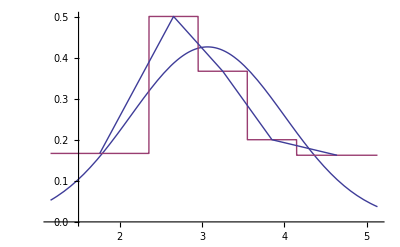

```mathematica
Show[Plot[{1/Sqrt[2π d] ⅇ^(-(t-a)^2/(2d)), gist[t]}, {t,1.16,5.13}],ListLinePlot[list]]
```

```mathematica
(*4.Нахождение доверительных интервалов*)
p= 0.95;
aI=Interval[{avg-Quantile[StudentTDistribution[Length[x]-1],(1+p)/2](√disp)/(√(n-1)),avg+Quantile[StudentTDistribution[Length[x]-1],(1+p)/2](√disp)/(√(n-1))}]
```

Interval[{2.79969,3.31231}]

```mathematica
σI=Interval[{(n disp)/Quantile[ChiSquareDistribution[n-1],(1+p)/2],(n disp)/Quantile[ChiSquareDistribution[n-1],(1-p)/2]}]
```

Interval[{0.56756,1.26305}]

```mathematica
(*  5. Проверка гипотезы о нормальном распределении с помощью критерия согласия Пирсона*)
```

```mathematica
ν = {};
p0 = {};
Clear[t];
For[i = 1, i≤Np,i++,
AppendTo[ν ,second[[i,5]]];
AppendTo[p0 ,∫_second[[i,2]]^second[[i,3]] 1/Sqrt[2π d] ⅇ^(-(t-avg)^2/(2disp))ⅆt ];
];
Print["Вектор частот попадания = ",ν ];
Print["Вектор вероятностей попадания в интервал при условии H_0 = ",p0 ];

t= ∑_(j=1)^Np ν[[j]]^2/(n p0[[j]]) - n;
Print["t=",t];
α = 0.05;
χ = 9.5;
If[t>=χ ,Print["Гипотеза отвергается"],Print["Гипотеза не отвергается"] ];
```

Вектор частот попадания = {10,15,11,6,8}

Вектор вероятностей попадания в интервал при условии H_0 = {0.190789,0.227489,0.245119,0.171549,0.0962896}

t=7.62692

Гипотеза не отвергается